```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mrussell/phd/gillespie

```mathematica
num=3;
q=1;
p=1.5;
α=100;
β=1.5;
```

```mathematica
S=Array[0.3&,num];
(*s=RandomReal[{0,1},num]*)
diag=Array[-(p+q)-S[[#]]&,num];
diag[[1]]=-p-S[[1]];
diag[[num]]=-q-β-S[[num]];
α1=SparseArray[{
Band[{2,1}]->p,
Band[{1,1}]->diag,
Band[{1,2}]->q
},{num,num}];
α1=Normal[α1];
```

```mathematica
β1=Array[0&,num];
β1[[1]]=α;
```

```mathematica
ClearAll[expn,expectation,expsystem,expinit]
```

```mathematica
expns[t_]:=Table[expn[i][t],{i,1,num}]
```

```mathematica
expsystem=D[expns[t],t]==α1.expns[t]+β1;
expns0=Array[150&,num];
expinit=expns[0]==expns0;
```

```mathematica
expectation=NDSolveValue[{expsystem,expinit},expns[t],{t,0,500},PrecisionGoal->100];
expectationfunc[t0_]:=expectation/.t->t0
```

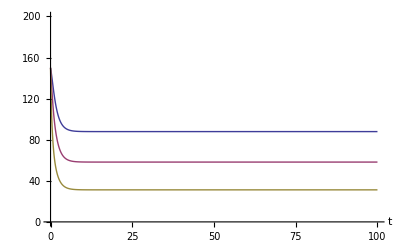

```mathematica
Plot[Evaluate[expectationfunc[t]],{t,0,100},AxesLabel->{t,Automatic},PlotRange->{0,200}]
```

```mathematica
expdata=Table[Join[{t},expectationfunc[t]],{t,0,50,0.05}];
```

```mathematica
Export["exp.dat",expdata,"Table","FieldSeparators"->" "]
```

exp.dat

```mathematica
a1mel[i_,j_,n_,s_,t_]:=Module[
{nf=Append[n,0]},
p(1-KroneckerDelta[i,1])(KroneckerDelta[i,j]-KroneckerDelta[i,j+1])n[[i-1]]+
(q(1-KroneckerDelta[i,1])(KroneckerDelta[i,j]-KroneckerDelta[i,j+1])+p(1-KroneckerDelta[i,num])(KroneckerDelta[i,j]-KroneckerDelta[i+1,j])+KroneckerDelta[i,j]s[[i]])n[[i]]+
q(1-KroneckerDelta[i,num])(KroneckerDelta[i,j]-KroneckerDelta[i+1,j])nf[[i+1]]+
KroneckerDelta[i,1]KroneckerDelta[j,1]α+
KroneckerDelta[i,num]KroneckerDelta[j,num]β n[[num]]
]
```

```mathematica
a1m[t_]:=Table[a1mel[i,j,expectationfunc[t],S,t],{i,1,num},{j,1,num}]
```

```mathematica
covs[t_]:=Table[cov[i][j][t],{i,1,num},{j,1,num}]
```

```mathematica
m[t_]:=α1.covs[t]
```

```mathematica
covsystem=D[covs[t],t]==a1m[t]+m[t]+Transpose[m[t]];
covs0=Table[100,{i,1,num},{j,1,num}];
```

```mathematica
covinit=covs[0]==covs0;
```

```mathematica
covariance=NDSolveValue[{covsystem,covinit},covs[t],{t,0,500},PrecisionGoal->100];
covariancefunc[t0_]:=covariance/.t->t0
```

```mathematica
Manipulate[ArrayPlot[covariancefunc[t],PlotRange->{0,200}],{t,0,50}]
```

```mathematica
Manipulate[covariancefunc[t]//MatrixForm,{t,0,500}]
```

```mathematica
covdata=covariancefunc[40];
```

```mathematica
Export["cov.dat",covdata,"FieldSeparators"->" "]
```

cov.dat

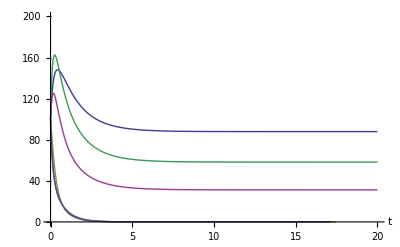

```mathematica
Plot[Evaluate[Extract[covariancefunc[t],{{1,1},{1,2},{1,3},{2,2},{2,3},{3,3}}]],{t,0,20},AxesLabel->{t,Automatic},PlotRange->{0,200}]
```

```mathematica
covdata=Table[Join[{t},Extract[covariancefunc[t],{{1,1},{1,2},{1,3},{2,2},{2,3},{3,3}}]],{t,0,50,0.05}];;
```

```mathematica
Export["cov.dat",covdata,"FieldSeparators"->" "]
```

cov.dat